## Biquad Filter

```mathematica
V=1;
τ=10^-5;
Q = 10;
```

```mathematica
ATP[ω_]:=-V/(1+ⅈ*ω*τ/Q+(ⅈ*ω*τ)^2)
ABP[ω_]:=-ATP[ω]*ⅈ*ω*τ
```

### Bodeplot

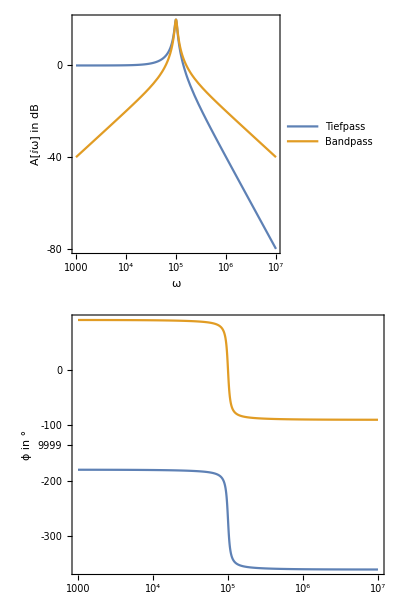

```mathematica
BodePlot[{ATP[ω], ABP[ω]}, {ω, 1000, 10000000},
ImageSize->Medium, FrameLabel->{{"ω", "A[ⅈω] in dB"},{" ", "ϕ in °"}}, PlotLegends->{"Tiefpass", "Bandpass"}]
```

### Ortskurve

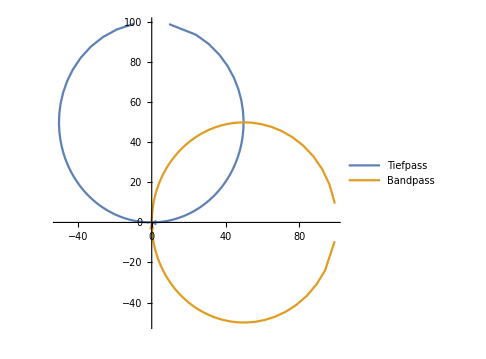

```mathematica
NyquistPlot[{ATP[ω], ABP[ω]}, {ω, 1000, 10000000},
ImageSize->Medium, PlotLegends->{"Tiefpass", "Bandpass"}]
```